# Hubbard parameters in Lieb lattice

## §Band Structure

```mathematica
ClearAll["Global`*"]
```

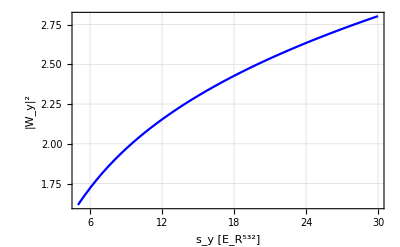

```mathematica
Off[General::spell1]
w1d=Import["C:\\Users\\hideki_2\\Documents\\Mathematica\\NumericalData\\LiebHubbard\\IntegratedWannierFunc.csv"]; (*load 1D optical lattice in y-axis*)
w4pow1D=Interpolation[w1d];
Plot[w4pow1D[x],{x,5,30},Frame->True,FrameLabel->{"s_y [E_R^532]","|W_y|^2","Wannier function in y-axis"},FrameStyle->Directive[Black,15,"Arial"],GridLines->Automatic,PlotStyle->Blue]
```

```mathematica
λ=1064 10^-9; (*Wave length*)
```

```mathematica
d = λ/2; (*Lattice const*)
```

```mathematica
as= 10.55 10^-9;
```

```mathematica
ℏ = 1.054571596 10^-34; (*Converted Plank const*)
```

```mathematica
kb = 1.3806503 10^-23; (*Boltzmann const*)
```

```mathematica
myb = 174 1.66053873 10^-27;(*Single atom mass of 174Yb*)
```

```mathematica
er = ℏ^2/(2 myb)((2 π)/λ)^2; (*Recoil energy of 1064nm lattice*)
```

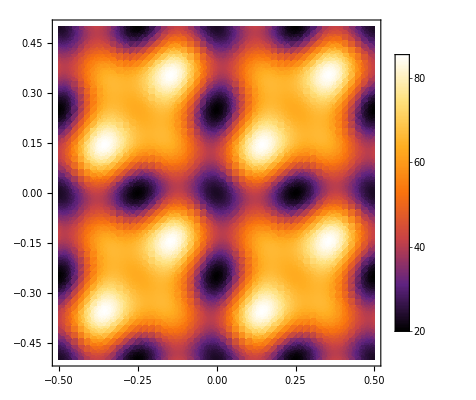

```mathematica
DensityPlot[v1(Sin[2 π x]^2 + Sin[2 π y]^2)+ v2 (Sin[2 π 2 x]^2 + Sin[2 π 2 y]^2) + v3 Sin[2 π (x- y) + π/2]^2 /. {v1 -> 20, v2 -> 20, v3 -> 23}, {x, -0.5,0.5}, {y, -0.5,0.5}, ColorFunction -> "SunsetColors",PlotLegends -> Automatic ,PlotPoints -> 50]
```

```mathematica
r=1;
n=4;
(* include (2n+1)^2 plane waves in calculation ↔ calculate over (2n+1)^2 bands *)
n2=10;(* calculate first n2 eigenvalues*)
m=8;(* calculate over (2m(+1))^2 quasimomenta *)
s1x= 13.;(* Subscript[V, 0]/Subscript[E, R], long lattice *)
s1z= 13.;(* Subscript[V, 0]/Subscript[E, R], long lattice *)
s2x=13.;(* Subscript[V, 0]/Subscript[E, R], short lattice *)
s2z=13.;(* Subscript[V, 0]/Subscript[E, R], short lattice *)
s3=15.5;(* Subscript[V, 0]/Subscript[E, R], diagonal lattice *)
ϕ=π/2;
h=Table[0,{i,1,(2n+1)^2},{j,1,(2n+1)^2}];(* Hamiltonian matrix for quasimomentum k (lattice spacing d=1)*)
Do[
If[(Abs[nx1-nx2]==1&&Abs[ny1-ny2]==0),h⟦(2n+1) (nx1+n)+(ny1+n)+1,(2n+1) (nx2+n)+(ny2+n)+1⟧=-s1x/4];
If[(Abs[nx1-nx2]==0&&Abs[ny1-ny2]==1),h⟦(2n+1) (nx1+n)+(ny1+n)+1,(2n+1) (nx2+n)+(ny2+n)+1⟧=-s1z/4];
If[(Abs[nx1-nx2]==2&&Abs[ny1-ny2]==0),h⟦(2n+1) (nx1+n)+(ny1+n)+1,(2n+1) (nx2+n)+(ny2+n)+1⟧=-s2x/4];
If[(Abs[nx1-nx2]==0&&Abs[ny1-ny2]==2),h⟦(2n+1) (nx1+n)+(ny1+n)+1,(2n+1) (nx2+n)+(ny2+n)+1⟧=-s2z/4];
(*If[nx1-nx2==1&&ny1-ny2==1,h⟦(2n+1) (nx1+n)+(ny1+n)+1,(2n+1) (nx2+n)+(ny2+n)+1⟧=-s3/4 ⅇ^(2ⅈ ϕ)];
If[nx1-nx2==-1&&ny1-ny2==-1,h⟦(2n+1) (nx1+n)+(ny1+n)+1,(2n+1) (nx2+n)+(ny2+n)+1⟧=-s3/4 ⅇ^(-2ⅈ ϕ)];*)
If[nx1-nx2==1&&ny1-ny2==-1,h⟦(2n+1) (nx1+n)+(ny1+n)+1,(2n+1) (nx2+n)+(ny2+n)+1⟧=-s3/4 ⅇ^(2ⅈ ϕ)];
If[nx1-nx2==-1&&ny1-ny2==1,h⟦(2n+1) (nx1+n)+(ny1+n)+1,(2n+1) (nx2+n)+(ny2+n)+1⟧=-s3/4 ⅇ^(-2ⅈ ϕ)];
If[nx1-nx2==0&&ny1-ny2==0,h⟦(2n+1) (nx1+n)+(ny1+n)+1,(2n+1) (nx2+n)+(ny2+n)+1⟧=((kx+2π nx1)^2+(ky+2π ny1)^2)/π^2+(s1x+s1z+s2x+s2z+s3)/2];
,{nx1,-n,n},{nx2,-n,n},{ny1,-n,n},{ny2,-n,n}]
MatrixForm[h];
Timing[e=Table[Eigensystem[SparseArray[N[h/.{kx->π((2(i-1))/(2m)-1),ky->π((2(j-1))/(2m)-1)}]],-n2],{i,1,2m+1},{j,1,2m+1}];]
e2=Table[Flatten[Table[{π((2(i-1))/(2m)-1),π((2(j-1))/(2m)-1),e⟦i,j,1,k⟧},{i,1,2m+1},{j,1,2m+1}],1],{k,1,n2(*(2n+1)^2*)}];
efit=Flatten[Table[e⟦i,j,1,-3;;-1⟧,{i,1,2m},{j,1,2m}],1];
(*efit=Flatten[Table[Eigenvalues[N[h/.{kx->π((2(i-1))/(2m)-1),ky->π((2(j-1))/(2m)-1)}],-3],{i,1,2m},{j,1,2m}],1];*)
bg12=Min[Abs[e2⟦-2,All,3⟧-e2⟦-1,All,3⟧]];
bg23=Min[Abs[e2⟦-3,All,3⟧-e2⟦-2,All,3⟧]];
bw1=Max[Abs[e2⟦-1,All,3⟧]]-Min[Abs[e2⟦-1,All,3⟧]];
bw2=Max[Abs[e2⟦-2,All,3⟧]]-Min[Abs[e2⟦-2,All,3⟧]];
bw3=Max[Abs[e2⟦-3,All,3⟧]]-Min[Abs[e2⟦-3,All,3⟧]];
```

{3.10938,Null}

-Graphics3D-

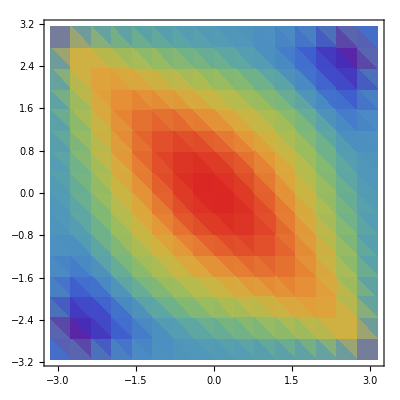

```mathematica
ListPlot3D[e2⟦-3;;-1⟧,PlotStyle->Thick,PlotRange->All,AspectRatio->1(*,InterpolationOrder->3*),ImageSize->300,ViewPoint->{1.3,1.7,0.1},Ticks->{{-Pi,-Pi/2,0,Pi/2,Pi},{-Pi,-Pi/2,0,Pi/2,Pi},Automatic},ColorFunction->"Rainbow", AxesStyle->Directive[Black,18, FontFamily -> "Cambria"]]
ListDensityPlot[e2⟦-2⟧,ColorFunction->"Rainbow"]
```

## §Caluculation of Bloch Wavefunction

```mathematica
ψ[p_,qx_,qy_,x_,y_]:=∑_(k=-n)^n ∑_(l=-n)^n (*Sign[e⟦qx+m+1,qy+m+1,2,-p⟧⟦(2n+1) (0+n)+(0+n)+1⟧]*)Normalize[e⟦qx+m+1,qy+m+1,2,-p⟧]⟦(2n+1) (k+n)+(l+n)+1⟧Exp[ⅈ( π/m qx+2π(k))x+ⅈ(π/m qy+2π(l)) y];
(*Normalized to the site number: ∫|ψ|^2 dx = N(=2m), pth band, quasimomentum -m≤q<m*)
p=1;
qx=0;
qy=0;
ck=Flatten[Table[{( π/m qx+2π(k))/(2π),( π/m qy+2π(l))/(2π),Abs[Normalize[e⟦qx+m+1,qy+m+1,2,-p⟧]⟦(2n+1) (k+n)+(l+n)+1⟧]^2},{k,-n,n},{l,-n,n}],1];
ck2=Table[Abs[Normalize[e⟦qx+m+1,qy+m+1,2,-p⟧]⟦(2n+1) (k+n)+(l+n)+1⟧]^2,{k,-n,n},{l,-n,n}];
(*ck=Table[{( π/m q+2π(k-n-1))/(2π),Abs[Normalize[e⟦q+m+1,2,2n+2-p⟧]⟦k⟧]^2},{k,1,2n+1}];*)
```

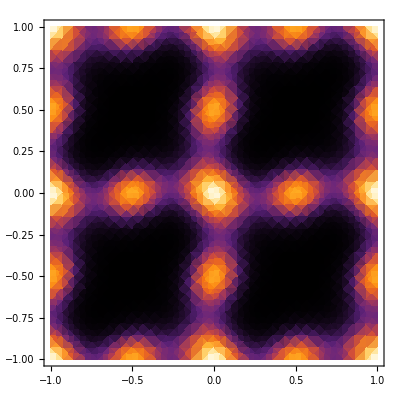

```mathematica
DensityPlot[Abs[ψ[1,qx,qy,x,y]]^2,{x,-1,1},{y,-1,1},ColorFunction->"SunsetColors",PlotRange->All]
```

## §Tight - Binding Model

```mathematica
Clear[ea,eb,taa,tbb,tab,tbc,tbc2]
htb={{ea-2taa (Cos[kx]+ Cos[ky]),-2tab Cos[kx/2],-2tab Cos[ky/2]},{-2tab Cos[kx/2],eb-2tbb (Cos[kx](*+ Cos[ky]*)),-2tbc  Cos[kx/2+ky/2]-2tbc2 Cos[kx/2-ky/2]},{-2tab Cos[ky/2],-2tbc  Cos[kx/2+ky/2]-2tbc2 Cos[kx/2-ky/2],eb-2tbb((* Cos[kx]+*) Cos[ky])}}(*/.{taa->0,tbb->0}*);
(*htb={{ea+38-2taa (Cos[kx]+ Cos[ky]),-tab (1+ⅇ^(ⅈ kx)),-tab (1+ⅇ^(-ⅈ ky))},{-tab (1+ⅇ^(-ⅈ kx)),eb+38-2tbb (Cos[kx]+ Cos[ky]),-tbc  (1+ⅇ^(-ⅈ kx-ⅈ ky))},{-tab (1+ⅇ^(ⅈ ky)),-tbc  (1+ⅇ^(ⅈ kx+ⅈ ky)),eb+38-2tbb( Cos[kx]+ Cos[ky])}}/.{taa->0,tbb->0};*)
TraditionalForm[htb]
```

(ea-2 taa (cos(kx)+cos(ky)) | -2 tab cos(kx/2) | -2 tab cos(ky/2)
-2 tab cos(kx/2) | eb-2 tbb cos(kx) | -2 tbc2 cos(kx/2-ky/2)-2 tbc cos(kx/2+ky/2)
-2 tab cos(ky/2) | -2 tbc2 cos(kx/2-ky/2)-2 tbc cos(kx/2+ky/2) | eb-2 tbb cos(ky))

```mathematica
(*initparams={(e⟦m+1,m+1,1,-3⟧-e⟦m+1,m+1,1,-1⟧)/(4 √2),Mean[Flatten[efit⟦All,{-3,-1}⟧]],Mean[Flatten[efit⟦All,-2⟧]],(Max[efit⟦All,-2⟧]-Min[efit⟦All,-2⟧])/4,-0.001,-0.001}*)
initparams={0.432363,27.232,27.0533,0.0605676,0.00174648,-0.0690442,-0.0201555}
paramsrp[p_]:={tab->p⟦1⟧,
(*Energy offset*)
ea->p⟦2⟧,eb->p⟦3⟧,
(*Diagonal hopping*)
tbc->p⟦4⟧,tbc2->p⟦5⟧,
(*Next-nearest hopping*)
taa->p⟦6⟧,
tbb->p⟦7⟧}
difstep=DiagonalMatrix[{0.001,0.002,0.002,0.0001,0.0001,0.00001,0.00001}];
maxstep={0.01,0.02,0.02,0.001,0.0005,0.0005,0.0005};
maxrec1=500;
maxrec2=50;
```

{0.432363,27.232,27.0533,0.0605676,0.00174648,-0.0690442,-0.0201555}

```mathematica
Dynamic[{j1,j2}]
Dynamic[params]
```

```mathematica
etbfit[p_]:=Flatten[Table[Eigenvalues[N[htb/.Join[{kx->π((2(i-1))/(2m)-1),ky->π((2(j-1))/(2m)-1)},paramsrp[p]]]],{i,1,2m},{j,1,2m}],1];
ediff[p_]:=Total[(etbfit[p]-efit)^2,2];
j1=0;
params=initparams;
diffcoeffs=Table[1,{i,1,Length[params]}];
hist={};
While[j1<maxrec1&&Norm[diffcoeffs]>10^-3,
diffcoeffs=Table[(ediff[params+difstep⟦i⟧]-ediff[params-difstep⟦i⟧])/(2difstep⟦i,i⟧),{i,1,Length[params]}];
α=Max[Abs[diffcoeffs/maxstep]]^-1;
params2=params-α diffcoeffs;
j2=0;
While[ediff[params2]>ediff[params]&&j2<maxrec2,
α=α/2;
params2=params-α diffcoeffs;
j2++;
];
params=params2;
AppendTo[hist,params];
j1++;
(*Print[{j1,j2,Norm[diffcoeffs]}];*)
]
(*fitres=FindMinimum[ediff,{{tab,3},{ea,1},{eb,-1},{tbc,3.5}(*,{taa,0.0001},{tbb,0.0001}*)}(*,Method->"PrincipalAxis"*)]*)
```

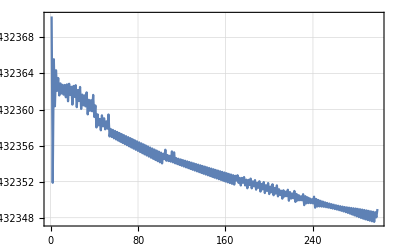
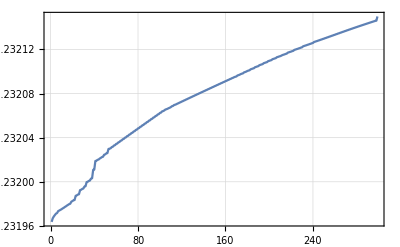
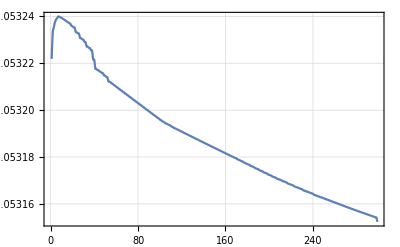
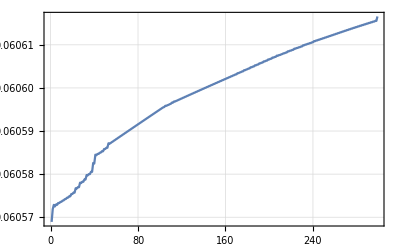
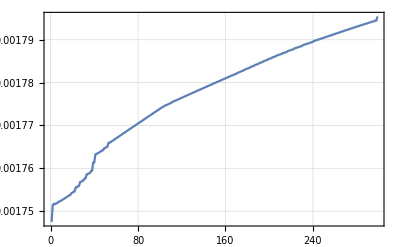
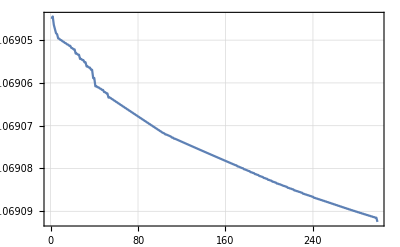
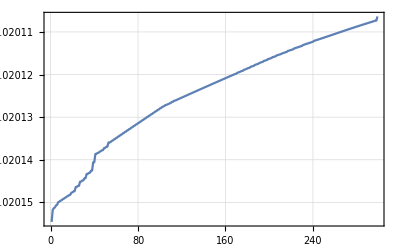

```mathematica
Table[ListLinePlot[hist⟦All,i⟧,Frame->True,GridLines->Automatic],{i,1,Length[hist⟦1⟧]}]
```

```mathematica
etb=Table[Eigensystem[N[htb/.Join[{kx->π((2(i-1))/(2m)-1),ky->π((2(j-1))/(2m)-1)},paramsrp[params]]]],{i,1,2m+1},{j,1,2m+1}];
etb2=Table[Flatten[Table[{π((2(i-1))/(2m)-1),π((2(j-1))/(2m)-1),etb⟦i,j,1,k⟧},{i,1,2m+1},{j,1,2m+1}],1],{k,1,3(*(2n+1)^2*)}];
u=etb⟦All,All,2⟧;
```

-Graphics3D-

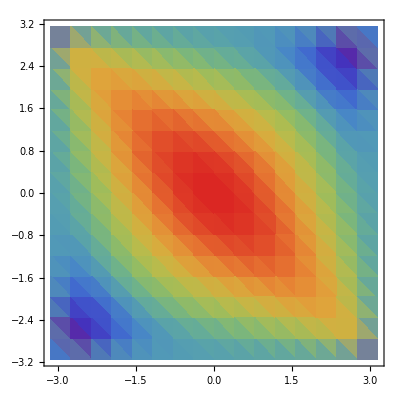

```mathematica
ListPlot3D[etb2⟦1;;3⟧,PlotRange->All,AspectRatio->1(*,InterpolationOrder->3*),ImageSize->300,ViewPoint->{1.3,1.7,0.1},Ticks->{{-Pi,-Pi/2,0,Pi/2,Pi},{-Pi,-Pi/2,0,Pi/2,Pi},Automatic},ColorFunction->"Rainbow",AxesStyle->Directive[Black,18, FontFamily -> "Cambria"]]
ListDensityPlot[etb2⟦-2⟧,ColorFunction->"Rainbow"]
```

## §Construction of Wannier Function

```mathematica
site={{0,0},{0.5,0},{0,0.5}};(*Stationaly phase*)
args=Table[1,{p,1,3},{i,1,2m+1},{j,1,2m+1}];
Timing[Do[
ampls=Table[Abs[∑_(l1=-n)^n ∑_(l2=-n)^n u⟦qx+m+1,qy+m+1,-p,sl⟧Normalize[e⟦qx+m+1,qy+m+1,2,-p⟧]⟦(2n+1) (l1+n)+(l2+n)+1⟧Exp[ⅈ( +2π(l1))site⟦sl,1⟧+ⅈ( +2π(l2))site⟦sl,2⟧]],{sl,1,3}];
If[Max[ampls]==ampls⟦1⟧,sl=1];
If[Max[ampls]==ampls⟦2⟧,sl=2];
If[Max[ampls]==ampls⟦3⟧,sl=3];
args⟦p,qx+m+1,qy+m+1⟧=Exp[-ⅈ Arg[∑_(l1=-n)^n ∑_(l2=-n)^n u⟦qx+m+1,qy+m+1,-p,sl⟧Normalize[e⟦qx+m+1,qy+m+1,2,-p⟧]⟦(2n+1) (l1+n)+(l2+n)+1⟧Exp[ⅈ( +2π(l1))site⟦sl,1⟧+ⅈ( +2π(l2))site⟦sl,2⟧]]];
,{p,1,3},{qx,-m,m-1},{qy,-m,m-1}]]
```

{9.0625,Null}

```mathematica
Timing[wannier1=Compile[{x,y},Evaluate[1/(2m)^2∑_(p=1)^3 ∑_(qx=-m)^(m-1) ∑_(qy=-m)^(m-1) ∑_(k=-n)^n ∑_(l=-n)^n args⟦p,qx+m+1,qy+m+1⟧u⟦qx+m+1,qy+m+1,-p,1⟧Normalize[e⟦qx+m+1,qy+m+1,2,-p⟧]⟦(2n+1) (k+n)+(l+n)+1⟧Exp[ⅈ( π/m qx+2π(k))x+ⅈ(π/m qy+2π(l)) y]]];
wannier2=Compile[{x,y},Evaluate[1/(2m)^2∑_(p=1)^3 ∑_(qx=-m)^(m-1) ∑_(qy=-m)^(m-1) ∑_(k=-n)^n ∑_(l=-n)^n args⟦p,qx+m+1,qy+m+1⟧u⟦qx+m+1,qy+m+1,-p,2⟧Normalize[e⟦qx+m+1,qy+m+1,2,-p⟧]⟦(2n+1) (k+n)+(l+n)+1⟧Exp[-ⅈ( π/m qx)0.5]Exp[ⅈ( π/m qx+2π(k))x+ⅈ(π/m qy+2π(l)) y]]];
wannier3=Compile[{x,y},Evaluate[1/(2m)^2∑_(p=1)^3 ∑_(qx=-m)^(m-1) ∑_(qy=-m)^(m-1) ∑_(k=-n)^n ∑_(l=-n)^n args⟦p,qx+m+1,qy+m+1⟧u⟦qx+m+1,qy+m+1,-p,3⟧Normalize[e⟦qx+m+1,qy+m+1,2,-p⟧]⟦(2n+1) (k+n)+(l+n)+1⟧Exp[-ⅈ( π/m qy)0.5]Exp[ⅈ( π/m qx+2π(k))x+ⅈ(π/m qy+2π(l)) y]]];]
```

{22.1875,Null}

```mathematica
grid=0.03;
Timing[wlist1=Flatten[Table[{x,y,wannier1[x,y]},{x,-1.,1.,grid},{y,-1.,1.,grid}],1];]
Timing[wlist2=Flatten[Table[{x,y,wannier2[x,y]},{x,-1.,1.,grid},{y,-1.,1.,grid}],1];]
Timing[wlist3=Flatten[Table[{x,y,wannier3[x,y]},{x,-1.,1.,grid},{y,-1.,1.,grid}],1];]
```

{24.70313,Null}

{22.6875,Null}

{21.14063,Null}

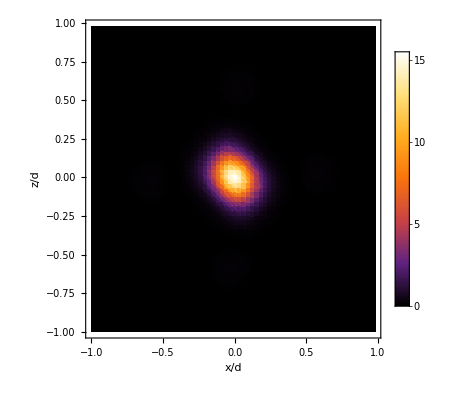

```mathematica
ListDensityPlot[Table[{wlist1⟦i,1⟧,wlist1⟦i,2⟧,Abs[wlist1⟦i,3⟧]^2},{i,1,Length[wlist1]}],PlotRange->All,ColorFunction->"SunsetColors",PlotLegends->Automatic,Frame->True, FrameLabel->{"x/d","z/d"}, FrameStyle->Directive[Black,20, FontFamily-> "Cambria"]]
```

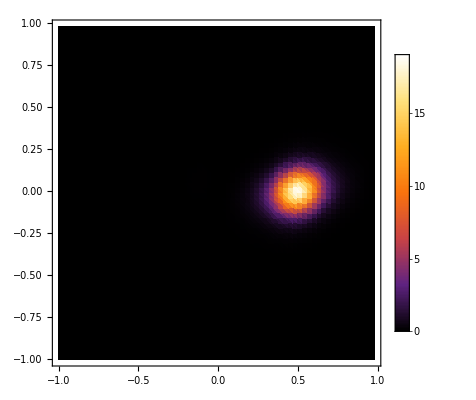

```mathematica
ListDensityPlot[Table[{wlist2⟦i,1⟧,wlist2⟦i,2⟧,Abs[wlist2⟦i,3⟧]^2},{i,1,Length[wlist2]}],PlotRange->All,ColorFunction->"SunsetColors",PlotLegends->Automatic, FrameStyle->Directive[Black,20, FontFamily -> "Cambria"]]
```

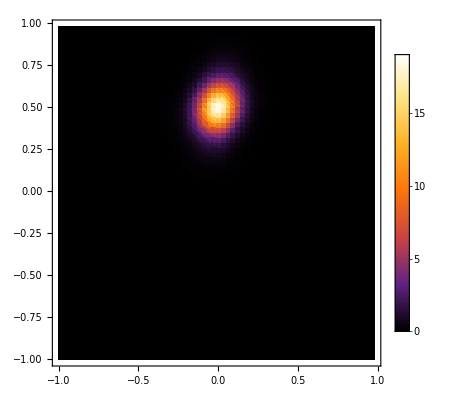

```mathematica
ListDensityPlot[Table[{wlist3⟦i,1⟧,wlist3⟦i,2⟧,Abs[wlist3⟦i,3⟧]^2},{i,1,Length[wlist3]}],PlotRange->All,ColorFunction->"SunsetColors",PlotLegends->Automatic,FrameStyle->Directive[Black,20, FontFamily -> "Cambria"]]
```

```mathematica
norm={∑_(i=1)^Length[wlist1] Abs[wlist1⟦i,3⟧]^2 grid^2,∑_(i=1)^Length[wlist2] Abs[wlist2⟦i,3⟧]^2 grid^2,∑_(i=1)^Length[wlist3] Abs[wlist3⟦i,3⟧]^2 grid^2}
```

{0.999324,0.998452,0.998452}

```mathematica
w4powLieb={1/norm⟦1⟧^2∑_(i=1)^Length[wlist1] Abs[wlist1⟦i,3⟧]^4 grid^2,1/norm⟦2⟧^2∑_(i=1)^Length[wlist2] Abs[wlist3⟦i,3⟧]^4 grid^2,1/norm⟦3⟧^2∑_(i=1)^Length[wlist3] Abs[wlist3⟦i,3⟧]^4 grid^2}
```

{7.30602,9.07811,9.07811}

```mathematica
as=5.6×10^-9;
s1d=15;(*2D confinement, unit of Subscript[E, R]^(532)*)
u=(4π ℏ^2 as)/myb 1/d^2 w4powLieb 1/(d/2)w4pow1D[s1d];
{u/er,10^-3 u/(2π ℏ),10^9 u/kb}
```

{{0.901443,1.12009,1.12009},{0.913025,1.13448,1.13448},{43.8183,54.4464,54.4464}}

```mathematica
Timing[wlist11d=Table[{x,wannier1[x,0]},{x,-1.2,1.2,0.02}];]
Timing[wlist21d=Table[{x,wannier2[x,0]},{x,-1.2,1.2,0.02}];]

Timing[wlist31d=Table[{x,wannier2[0,x]},{x,-1.2,1.2,0.02}];]
```

{0.65625,Null}

{0.59375,Null}

{0.57813,Null}

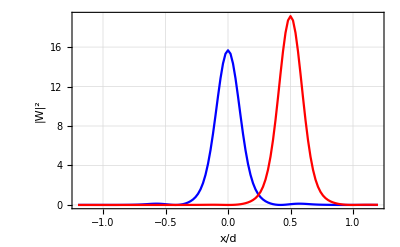

```mathematica
ListLinePlot[{Table[{wlist11d⟦i,1⟧,Abs[wlist11d⟦i,2⟧]^2},{i,1,Length[wlist11d]}],Table[{wlist21d⟦i,1⟧,Abs[wlist21d⟦i,2⟧]^2},{i,1,Length[wlist21d]}](*,Table[{wlist31d⟦i,1⟧,Abs[wlist31d⟦i,2⟧]^2},{i,1,Length[wlist31d]}]*)},PlotRange->All,Frame->True,Axes->None,GridLines->Automatic,FrameLabel->{"x/d","|W|^2"},FrameStyle->Directive[Black,20,FontFamily->"Calibri"],PlotStyle->{Blue,Red}]
```

```mathematica
onsite={};
Do[
AppendTo[onsite,{s1d,(4π ℏ^2 as)/(er myb)1/d^2 w4powLieb ⟦1⟧1/(d/2)w4pow1D[s1d],(4π ℏ^2 as)/(er myb)1/d^2 Mean[w4powLieb⟦2;;3⟧] 1/(d/2)w4pow1D[s1d]}]
,{s1d,5,30,0.5}]
```

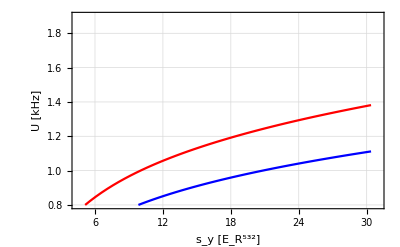

```mathematica
ListLinePlot[{onsite⟦All,{1,2}⟧*er/(2*π*ℏ)/10^3,onsite⟦All,{1,3}⟧*er/(2*π*ℏ)/10^3},Frame->True,Axes->None,GridLines->Automatic,FrameLabel->{"s_y [E_R^532]","U [kHz]"},FrameStyle->Directive[Black,20,FontFamily->"Calibri"],PlotStyle->{Blue,Red}, PlotRange->{{4.5,31},{0.8,1.9}}]
```

```mathematica
(4π ℏ^2 as)/(er myb)1/d^2 w4powLieb ⟦1⟧1/(d/2)w4pow1D[10]
```

0.797218

```mathematica
w4powLieb ⟦2⟧/w4powLieb ⟦1⟧
```

1.24255

```mathematica
(4π ℏ^2 as)/(er myb)1/d^3 w4powLieb ⟦1⟧*er/(2*π*ℏ)/10^3
```

0.198354

```mathematica
(4π ℏ^2 as)/(er myb)1/d^2 w4powLieb ⟦2⟧
```

1.29456×10^-7

```mathematica
ediff[params]
```

0.127435